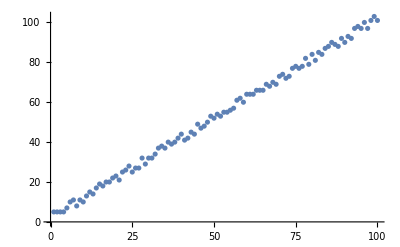

```mathematica
ListPlot[Table[k+RandomInteger[4],{k,100}]]
```

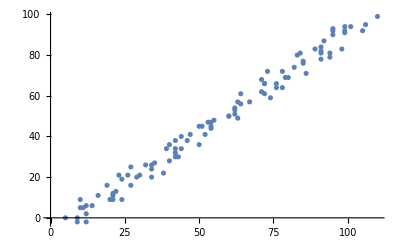

```mathematica
ListPlot[Table[{k+RandomInteger[10],k-RandomInteger[6]},{k,100}]]
```

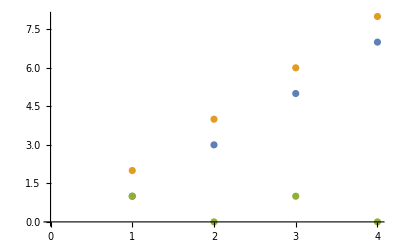

```mathematica
ListPlot[{{1,3,5,7},{2,4,6,8},{1,0,1,0}}]
```

```mathematica
ListPlot[Callout[#,IntegerName[10^#]]&/@Range[0,30,3]]
```

-Graphics-

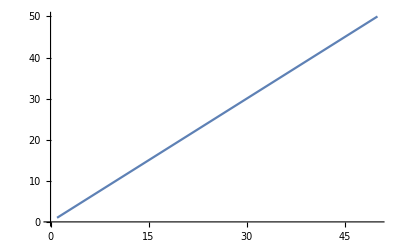

```mathematica
ListLinePlot[Range[50]]
```

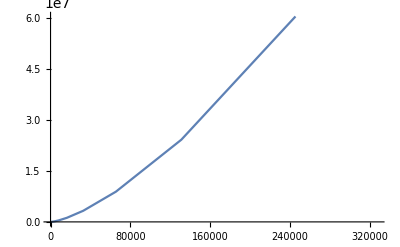

```mathematica
ListLinePlot[Table[{2^k,Exp[k]},{k,20}]]
```

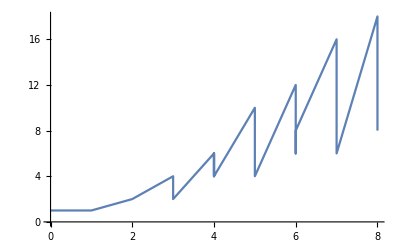

```mathematica
ListLinePlot[Table[{PrimePi[k],EulerPhi[k]},{k,20}]]
```

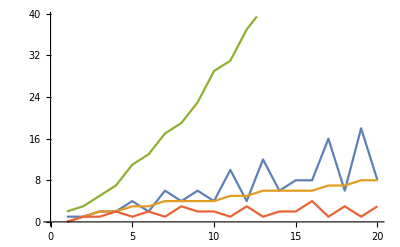

```mathematica
ListLinePlot[Table[{k,f[k]},{f,{EulerPhi,PrimePi,Prime,PrimeOmega}},{k,20}]]
```

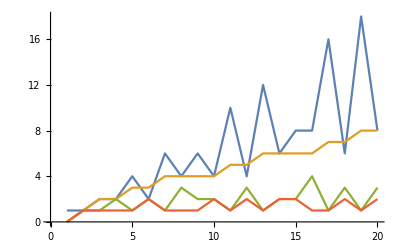

```mathematica
ListLinePlot[Table[{k,f[k]},{f,{EulerPhi,PrimePi,PrimeOmega,PrimeNu}},{k,20}]]
```

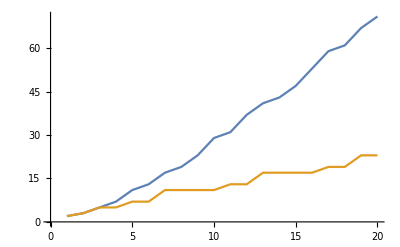

```mathematica
ListLinePlot[Table[{k,f[k]},{f,{Prime,NextPrime}},{k,20}]]
```

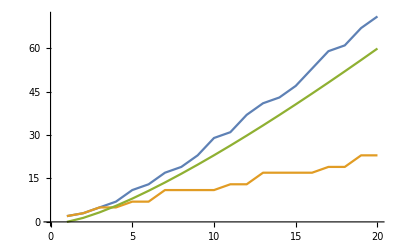

```mathematica
ListLinePlot[Table[{k,f[k]},{f,{Prime,NextPrime,# Log[#]&}},{k,20}]]
```

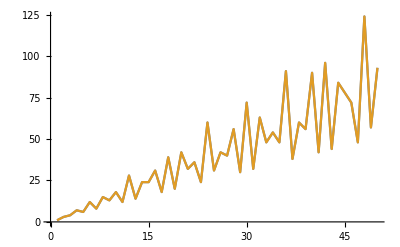

```mathematica
ListLinePlot[Table[{k,f[k]},{f,{DivisorSigma[1,#]&,DivisorSum[#,#&]&}},{k,50}]]
```

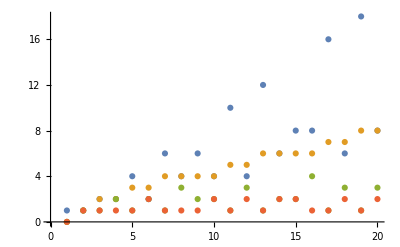

```mathematica
ListPlot[Table[{k,f[k]},{f,{EulerPhi,PrimePi,PrimeOmega,PrimeNu}},{k,20}]]
```

```mathematica
ListLinePlot[Table[{k,f[k]},{f,{EulerPhi,PrimePi,PrimeOmega,PrimeNu}},{k,20}]]
```

-Graphics-

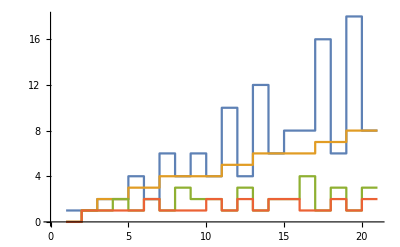

```mathematica
ListStepPlot[Table[{k,f[k]},{f,{EulerPhi,PrimePi,PrimeOmega,PrimeNu}},{k,20}]]
```

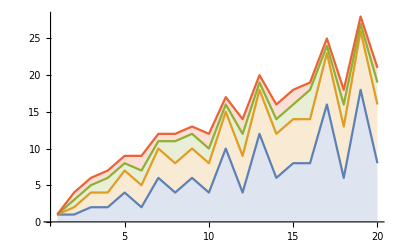

```mathematica
StackedListPlot[Table[{k,f[k]},{f,{EulerPhi,PrimePi,PrimeOmega,PrimeNu}},{k,20}]]
```

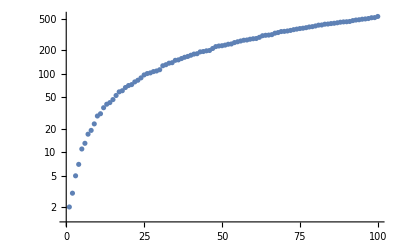

```mathematica
ListLogPlot[Table[{k,Prime[k]},{k,100}]]
```

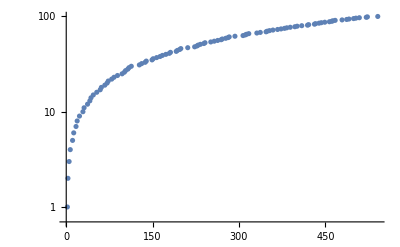

```mathematica
ListLogPlot[Table[{Prime[k],k},{k,100}]]
```

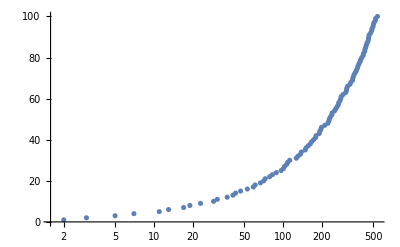

```mathematica
ListLogLinearPlot[Table[{Prime[k],k},{k,100}]]
```

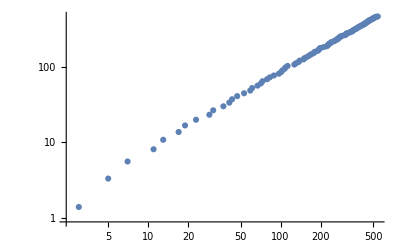

```mathematica
ListLogLogPlot[Table[{Prime[k],Log[k]k},{k,100}]]
```

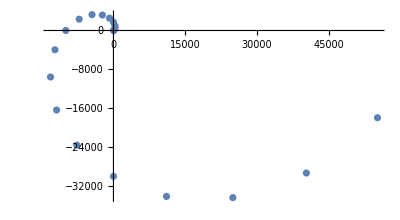

```mathematica
ListPolarPlot[Table[2+3k+5 k^2+7 k^3,{k,20}]]
```

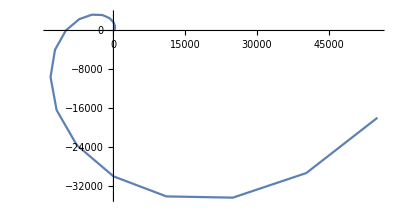

```mathematica
ListPolarPlot[Table[2+3k+5 k^2+7 k^3,{k,20}],Joined->True]
```

```mathematica
ListPlot3D[Table[{Sin[k],Cos[k],Tan[k]},{k,20}]]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[{1+2k+3 k^2+5 k^3,Prime[k],Log[k]},{k,20}]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Table[{1+2k1,Prime[k2],Log[k2]},{k1,20},{k2,20}]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Table[{EulerPhi[k1],k,PrimeOmega[k]},{k1,20},{k,20}]]
```

-Graphics3D-

```mathematica
ListLinePlot3D[Table[{EulerPhi[k1],k,PrimeOmega[k]},{k1,20},{k,20}]]
```

-Graphics3D-

```mathematica
ListLinePlot3D[Table[{EulerPhi[k1],k,PrimeOmega[k]},{k1,20},{k,20}],Filling->Bottom]
```

-Graphics3D-

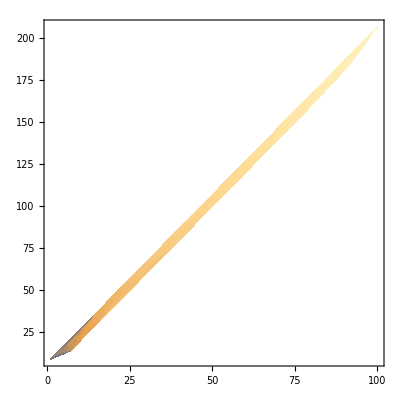

```mathematica
ListDensityPlot[Table[{k,2k+RandomInteger[7],Log[k]},{k,100}]]
```

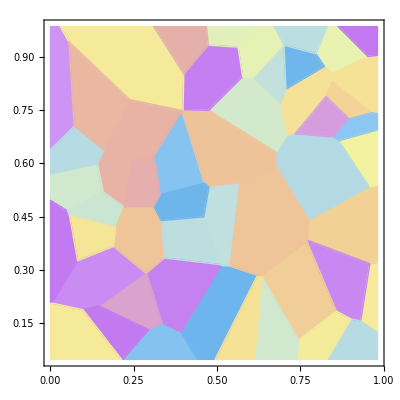

```mathematica
ListDensityPlot[RandomReal[1,{50,3}],InterpolationOrder->0,ColorFunction->"Pastel",BoundaryStyle->Black]
```

```mathematica
ListDensityPlot3D[RandomReal[1,{50,4}],ColorFunction->"Pastel"]
```

-Graphics3D-

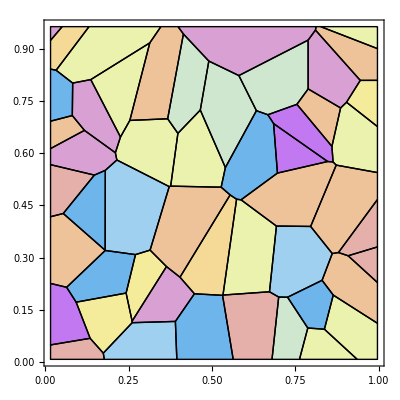

```mathematica
ListContourPlot[RandomReal[1,{50,3}],InterpolationOrder->0,ColorFunction->"Pastel",BoundaryStyle->Black]
```

```mathematica
ListContourPlot3D[RandomReal[1,{50,4}],ColorFunction->"Pastel",BoundaryStyle->Black]
```

-Graphics3D-

```mathematica
ListSliceDensityPlot3D[RandomReal[NormalDistribution[70,24],{5000,4}]]
```

-Graphics3D-

```mathematica
ListSliceContourPlot3D[RandomReal[NormalDistribution[70,24],{5000,4}]]
```

-Graphics3D-

I like ListSliceContourPlot

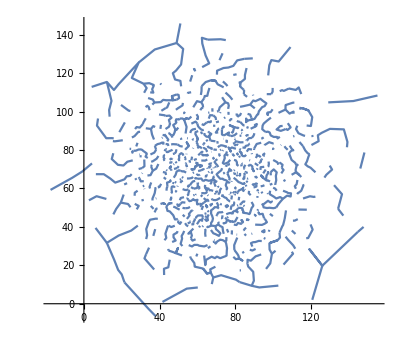

```mathematica
ListCurvePathPlot[RandomReal[NormalDistribution[70,24],{2000,2}]]
```

```mathematica
ListSurfacePlot3D[RandomReal[NormalDistribution[70,24],{2000,3}]]
```

-Graphics3D-

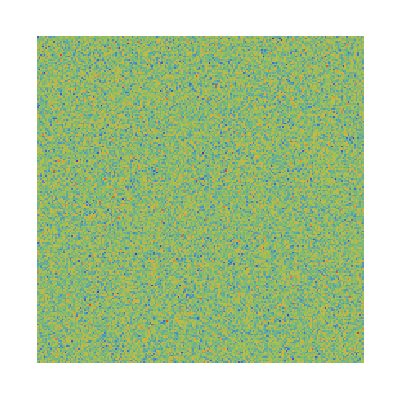

```mathematica
ArrayPlot[RandomReal[NormalDistribution[70,15],{200,200}],ColorFunction->"Rainbow"]
```

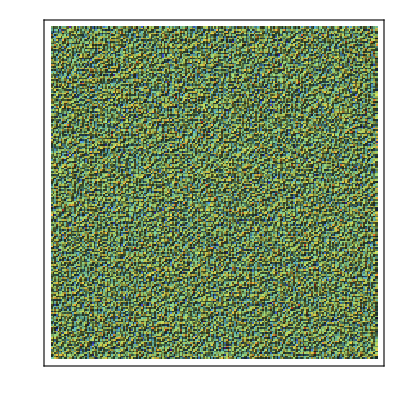

```mathematica
ReliefPlot[RandomReal[NormalDistribution[70,15],{200,200}],ColorFunction->"Rainbow"]
```

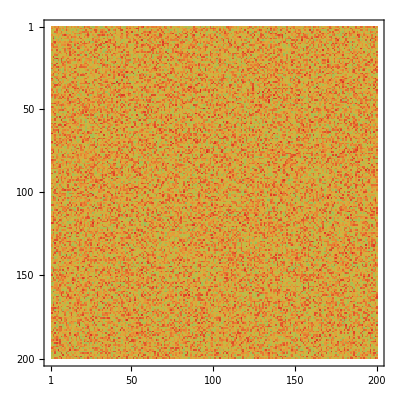

```mathematica
MatrixPlot[RandomReal[NormalDistribution[70,15],{200,200}],ColorFunction->"Rainbow"]
```

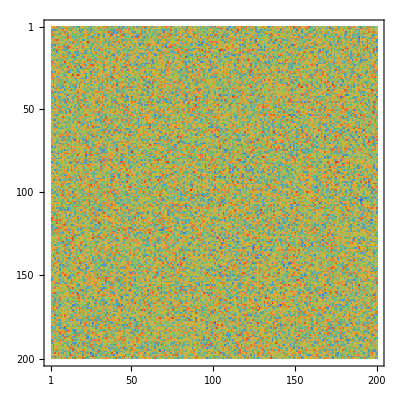

```mathematica
MatrixPlot[RandomReal[NormalDistribution[70,150],{200,200}],ColorFunction->"Rainbow"]
```

```mathematica
ArrayPlot3D[RandomReal[NormalDistribution[70,150],{20,20,20}],ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
RadialAxisPlot[RandomReal[NormalDistribution[100,43],{40}]]
```

-Graphics-

```mathematica
RadialAxisPlot[RandomReal[NormalDistribution[100,43],{40,5}]]
```

-Graphics-

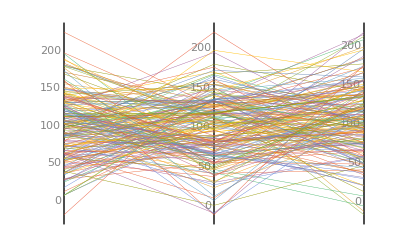

```mathematica
ParallelAxisPlot[RandomReal[NormalDistribution[100,43],{40,5,3}]]
```

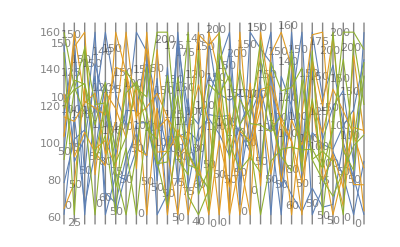

```mathematica
ParallelAxisPlot[RandomReal[NormalDistribution[100,43],{3,5,30}]]
```

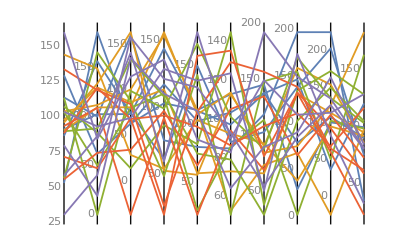

```mathematica
ParallelAxisPlot[RandomReal[NormalDistribution[100,43],{5,5,10}]]
```

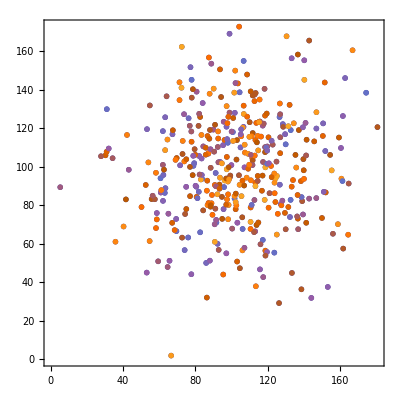

```mathematica
PointValuePlot[Table[RandomReal[NormalDistribution[100,30],2]->RandomReal[],400]]
```

```mathematica
FeatureSpacePlot[RandomColor[500]]
```

-Graphics-

```mathematica
#["Image"]&/@RandomEntity["Polyhedron",6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FeatureSpacePlot3D[#["Image"]&/@RandomEntity["Polyhedron",6]]
```

-Graphics3D-

```mathematica
FeatureSpacePlot3D[#["Image"]&/@RandomEntity["Polyhedron",20]]
```

-Graphics3D-

```mathematica
DateObject[{100,50,20}]
```

Wed 20 Feb 104

```mathematica
RandomInteger[{1000,2000},24]
```

{1100,1344,1110,1741,1292,1769,1134,1773,1422,1393,1892,1833,1532,1708,1960,1282,1057,1642,1818,1717,1394,1329,1221,1727}

```mathematica
DateObject/@Transpose@{RandomInteger[{1000,2000},24],RandomInteger[{1,12},24],RandomInteger[{1,30},24]}
```

{Sun 15 Apr 1928,Sat 5 May 1951,Thu 19 Sep 1135,Sat 11 Dec 1441,Sun 26 Nov 1139,Thu 17 Oct 1343,Thu 8 Apr 1238,Tue 22 Oct 1833,Tue 5 Oct 1143,Mon 3 Nov 1794,Wed 20 Nov 1861,Fri 12 May 1284,Sun 16 Nov 1681,Mon 13 Sep 1351,Thu 28 Jun 1314,Mon 20 Feb 1347,Sun 9 Apr 1944,Tue 15 Nov 1340,Sat 5 Aug 1656,Sun 16 Mar 1281,Sat 27 Oct 1004,Sun 20 May 1764,Thu 22 Apr 1909,Sat 18 Aug 1629}

```mathematica
Partition[Transpose@{RandomInteger[{1000,2000},24],RandomInteger[{1,12},24],RandomInteger[{1,30},24]},2]
```

{{{1601,1,29},{1237,6,21}},{{1449,2,25},{1022,9,21}},{{1691,4,6},{1172,5,22}},{{1981,3,21},{1343,10,23}},{{1237,1,22},{1498,5,26}},{{1201,1,25},{1584,11,1}},{{1660,8,23},{1922,8,9}},{{1741,3,21},{1358,11,27}},{{1523,9,1},{1282,1,14}},{{1670,6,3},{1797,10,24}},{{1737,12,14},{1311,3,28}},{{1931,4,17},{1178,6,15}}}

```mathematica
Map[DateObject,Partition[Transpose@{RandomInteger[{1000,2000},24],RandomInteger[{1,12},24],RandomInteger[{1,30},24]},2],{2}]
```

{{Wed 18 May 1403,Thu 19 Dec 1878},{Wed 27 May 1592,Sat 20 May 1617},{Sat 30 Dec 1228,Wed 6 Sep 1995},{Fri 16 Jan 1367,Wed 12 Aug 1293},{Thu 19 Dec 1512,Thu 29 Oct 1485},{Thu 7 Oct 1926,Fri 29 Nov 1405},{Tue 6 Apr 1728,Tue 9 Jun 1626},{Sun 7 Jul 1196,Sun 30 Aug 1435},{Tue 23 Feb 1954,Tue 13 Apr 1249},{Tue 14 Jun 1403,Mon 27 Jun 1538},{Wed 22 May 1996,Fri 15 Oct 1841},{Fri 28 Mar 1856,Tue 13 Jan 1085}}

```mathematica
DateInterval/@Map[DateObject,Partition[Transpose@{RandomInteger[{1000,2000},24],RandomInteger[{1,12},24],RandomInteger[{1,30},24]},2],{2}]
```

{DateInterval[…],DateInterval[…],DateInterval[…],DateInterval[…],DateInterval[…],DateInterval[…],DateInterval[…],DateInterval[…],DateInterval[…],DateInterval[…],DateInterval[…],DateInterval[…]}

```mathematica
TimelinePlot[DateInterval/@Map[DateObject,Partition[Transpose@{RandomInteger[{1000,2000},24],RandomInteger[{1,12},24],RandomInteger[{1,30},24]},2],{2}]]
```

-Graphics-

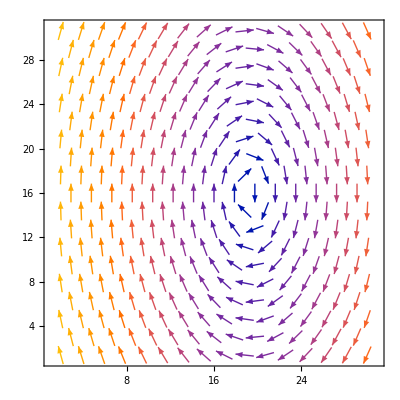

```mathematica
ListVectorPlot[Table[{y,-3x+2},{x,-3,3,0.2},{y,-3,3,0.2}]]
```

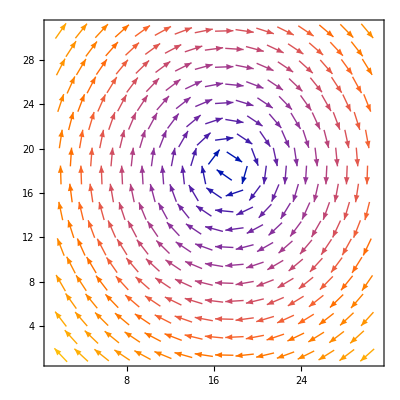

```mathematica
ListVectorPlot[Table[{7y-3,-8x+2},{x,-3,3,0.2},{y,-3,3,0.2}]]
```

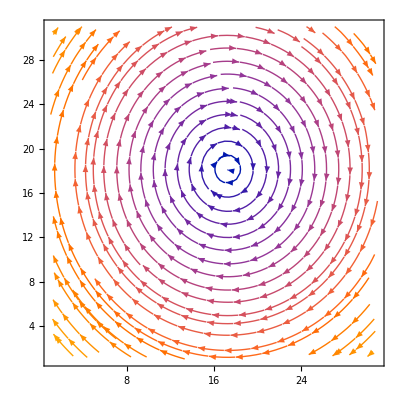

```mathematica
ListStreamPlot[Table[{7y-3,-8x+2},{x,-3,3,0.2},{y,-3,3,0.2}]]
```

```mathematica
ListStreamPlot3D[Table[{7y-3,-8x+2,z},{x,-3,3,0.2},{y,-3,3,0.2},{z,0,5}]]
```

-Graphics3D-

```mathematica
ListVectorPlot3D[Table[{7y-3,-8x+2,z},{x,-3,3,0.2},{y,-3,3,0.2},{z,0,5}]]
```

-Graphics3D-

```mathematica
ListSliceVectorPlot3D@Table[{y,-x,z},{z,-3,3},{y,-2,2},{x,-2,2}]
```

-Graphics3D-

```mathematica
ListSliceVectorPlot3D@Table[{y,-x+y,z+x},{z,-3,3},{y,-2,2},{x,-2,2}]
```

-Graphics3D-

```mathematica
ExampleData[]
```

{AerialImage,Audio,ColorTexture,Dataset,Geometry3D,LinearOptimization,LinearProgramming,MachineLearning,Matrix,NetworkGraph,Sound,SpatialPointData,Statistics,TestAnimation,TestImage,TestImage3D,TestImageSet,Text,Texture}

```mathematica
ExampleData["Text"]
```

{{Text,AeneidEnglish},{Text,AeneidLatin},{Text,AliceInWonderland},{Text,BeowulfModern},{Text,BeowulfOldEnglish},{Text,CodeOfHammurabiEnglish},{Text,DeclarationOfIndependence},{Text,DonQuixoteIEnglish},{Text,DonQuixoteISpanish},{Text,FaustI},{Text,FederalistTen},{Text,FriendsRomansCountrymen},{Text,GenesisKJV},{Text,GettysburgAddress},{Text,Hamlet},{Text,HomerOdysseyGreek},{Text,JFKInaugural},{Text,LesFleursDuMal},{Text,LoremIpsum},{Text,MagnaCarta},{Text,OnTheNatureOfThingsEnglish},{Text,OriginOfSpecies},{Text,PlatoMenoEnglish},{Text,PrideAndPrejudice},{Text,Prufrock},{Text,ShakespearesSonnets},{Text,TaoTehChingChinese},{Text,TheRaven},{Text,ToBeOrNotToBe},{Text,UNHumanRightsChinese},{Text,UNHumanRightsDanish},{Text,UNHumanRightsDutch},{Text,UNHumanRightsEnglish},{Text,UNHumanRightsEsperanto},{Text,UNHumanRightsFrench},{Text,UNHumanRightsGerman},{Text,UNHumanRightsGreek},{Text,UNHumanRightsHawaiian},{Text,UNHumanRightsIndonesian},{Text,UNHumanRightsIrish},{Text,UNHumanRightsJapanese},{Text,UNHumanRightsKorean},{Text,UNHumanRightsLatin},{Text,UNHumanRightsMaori},{Text,UNHumanRightsRussian},{Text,UNHumanRightsScottishGaelic},{Text,UNHumanRightsSpanish},{Text,UNHumanRightsSwahili},{Text,UNHumanRightsSwedish},{Text,USConstitution}}

```mathematica
ExampleData[{"Text","UNHumanRightsChinese"}]
```

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[Null,Whitespace→ ].

StringReplace[Null,Whitespace→ ]

```mathematica
WordCloud[RandomChoice[{"boy","girl"},30]]
```

-Graphics-

```mathematica
ChromaticityPlot["RGB"]
```

-Graphics-

```mathematica
ChromaticityPlot["LUV"]
```

-Graphics-

```mathematica
ChromaticityPlot3D["LUV"]
```

-Graphics3D-

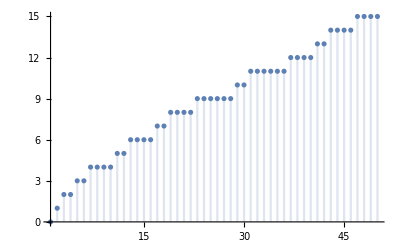

```mathematica
DiscretePlot[PrimePi[k],{k,1,50}]
```

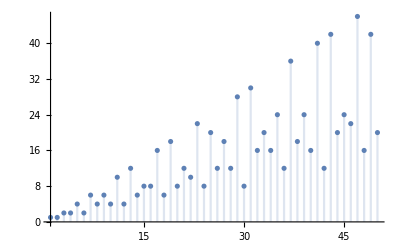

```mathematica
DiscretePlot[EulerPhi[k],{k,1,50}]
```